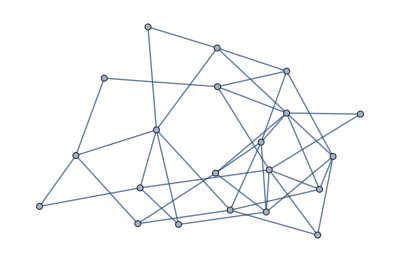

```mathematica
(*
	尝试复现网络设置：20 个路由节点构成的随机网络，链路容量为C = 5（Gbps），并保证任意两个节点之间都存在路径。业务设置：业务流数目由0 到500 逐步增加,每条业务流随机选择起始节点和目的节点，按照Dijaska算法进行选路。业务的带宽需求满足正态分布D~N(2,0.3)。 在无差别网络中，业务的优先级设定为 =1；在有差别网络中，业务的优先级分为3个等级 =1，2，3，并随机分配业务优先级。
*)

(*全局设置*)

j = 0;
TotalStreams = 15;

(********************************************************)

(*准备*)
(*为表示单条业务的三个属性带宽、优先级、经过的边以及顶点分别构建一个list，用来存储每条业务信息！*)

StreamEdges={};
StreamPaths = {};
StreamPriorities = {};
StreamBandwidths={};

(*一、业务层网络拓扑生成*)
(*1、首先生成一个20顶点，且确定连通的路由图（完成）*)
ClearAll;
flag = 0;

While[flag== 0,
d=RandomGraph[BernoulliGraphDistribution[21,0.2]];
flag =If [d.ConnectedGraphQ,1,0];
];


(*2、链路容量，负载设置（完成）*)

BWGenerate = Table[5 , EdgeCount[d]];
LoadGenerate = Table[0 , EdgeCount[d]];
graph = Graph[EdgeList[d],EdgeCapacity->BWGenerate]
PropertyValue[{graph,EdgeList[graph]},"CurrentLoad"] = 0;

(*二、单条业务的构建*)
While [j++<TotalStreams ,
(*1、随机构建一个业务的起点和终点（完成）*)

Startpoint = RandomInteger[{1,20}];
flag=0;
While[flag==0,
Endpoint = RandomInteger[{1,20}];
flag = If[Startpoint != Endpoint,1,0]];

(*2、随机构建业务流带宽，以及优先级，并根据容量选择最短路*)

While[,
Bandwidth = RandomReal[NormalDistribution[1,0.3]];
If[Bandwidth>0,Break,Continue]];
Priority=RandomInteger[{1,3}];

(*难点：选择一条容量能够支持业务的最短路*)
CurrentPath = FindShortestPath[graph,Startpoint,Endpoint];

tempGraph =graph;
While[,
flag=1;
subg = Subgraph[graph,CurrentPath];

i=0;
SubEdgeList=EdgeList[subg];
(*内循环，看当前选路是否满足带宽需求，如某边不满足则摒弃该边，重选路*)
While[++i≤ EdgeCount[subg],

flag =  If[PropertyValue[{graph,SubEdgeList[[i]]},EdgeCapacity]≥ Bandwidth,1,0];
(*此处flag为0时表示当前选路不能满足要求，跳出内循环*)
If[flag==0,Break];
]
If[flag==1,Break]
(*flag为0时重新选路*);
tempGraph = EdgeDelete[tempGraph,SubEdgeList[[i]]];
CurrentPath=  FindShortestPath[tempGraph,Startpoint,Endpoint];
If[CurrentPath=={},{Print["NO ROUTE"]，Break}]
]
(*3、把graph中负载情况进行修改*);
i=0;
subg = Subgraph[graph,CurrentPath];
SubEdgeList=EdgeList[subg];
While[++i≤ EdgeCount[subg],
{
PropertyValue[{graph,SubEdgeList[[i]]},"CurrentLoad"] = PropertyValue[{graph,SubEdgeList[[i]]},"CurrentLoad"]  + Bandwidth
}
];
(*4、单条业务的三个属性进行整理*)

StreamPaths = Append[StreamPaths,CurrentPath];
StreamPriorities = Append[StreamPriorities,Priority];
StreamBandwidths = Append[StreamBandwidths,Bandwidth];
StreamEdges=Append[StreamEdges,EdgeList[Subgraph[graph,StreamPaths[[j]]]]];
]
```

```mathematica
截至目前完成了：
一、业务层网络的随机拓扑生成，设置每条链路的容量，并实时存储其的负载；
二、随机生成N个业务，在一定概率模型下定义其起终点，带宽，以及优先度；
三、根据D算法从最近路径开始找起，根据链路容量状态确认选路，并更新链路状态；

还要做：
一、根据业务的分布情况，按照业务之间的耦合关系构建上层流网络，并在其中反映耦合的紧密程度；
二、设定故障逻辑；
	1、多类随机初次故障产生（随机、故意、局部、全局、先后、同时）；
	2、级联故障的模拟：
		（1）业务层拓扑层面上，即邻接路由节点的相互作用；
		（2）上层流网络拓扑中，相邻业务节点之间的相互作用；
三、可靠性的评价；
四、保护线路的设置；

后续工作的一些想法：
一、反映业务耦合紧密程度时可以用到的一些特征：
	1、两条业务之间共用的链路（边）的个数；
	2、带宽的大小；
二、故障的表示；
	1、给顶点加自定义属性，表示好坏；
	2、在后续，如要考虑重新选路，或是检测网络连通性等情况时，用删去故障点的子图进行分析；
三、故障的传播；
	目前暂且先只考虑依照一定概率进行；
四、局部打击的逻辑实现；
	目前考虑随机选取一个点，相邻节点进行概率判定决定是否同样故障，总体数量服从某种概率分布？
五、可靠性评价；
	具体评价措施等待之后完成初步模型后完善；
六、保护线路的设置；
	完成初步模型后与顾老师商量。
```

```mathematica
(*四、根据业务的分布情况，按照业务之间的耦合关系构建上层流网络，并在其中反映耦合的紧密程度；*)

(*先准备点图，即有多少个业务就有多少个点*)

TopGraph=Graph[Table[i,{i,Length[StreamPaths]}],{}];

(*遍历前n-1个业务*)
i=1;
While [i<Length[StreamPaths],{
(*与A业务的序号后续业务分别进行比对*)
j=i+1;
counter=0;
While[j≤ Length[StreamPaths],{
(*比对时是遍历A业务的每条边，看是否在其序号后续的业务B是否存在这条边*)
k=1;
While[k≤ Length[EdgeList[Subgraph[graph,StreamPaths[[i]]]]],{
If[MemberQ[StreamEdges[[j]],StreamEdges[[i]][[k]]],counter++];
k++;
}];
(*业务A与业务B之间的比对完毕，这时候的counter里面存的就是二者之间共有的链路长度*)
If[counter≥1,{
(*此处用标签表示业务之间耦合程度的强弱*)
TopGraph=Graph[EdgeAdd[TopGraph,UndirectedEdge[i,j]],EdgeLabels->{UndirectedEdge[i,j]-> counter}]
}];
j++;
}];
i++;
}]

TopGraph
```

```mathematica
(*五、故障逻辑的设置;
	1、多类随机初次故障产生（随机、故意、局部、全局、先后、同时）;*)

(*六类故障情形：随机局部同时（1），故意局部同时（2），随机全局同时（3），故意全局同时（4），
			   随机局部先后（5），故意局部先后（6），随机全局先后（7），故意全局先后（8）；*)

ProblemType = 0;

(*先去做一个单个节点随机故障试试水？*)

If[ProblemType==0,{
(*随机选取一个路由节点进行打击*)
HitPoint =RandomInteger[{1,20}];
i=7;
}];


(*	2、级联故障的模拟：
		（1）业务层拓扑层面上，即邻接路由节点的相互作用;
		（2）上层流网络拓扑中，相邻业务节点之间的相互作用;*)
```